```mathematica
wavelengthCylindricalInterferometer=658.0   *10^-9 (*Multiply by interferometer wavelength,units:data *);
```

## NIL1003Index3

### NIL-Sample2-Concave-20221116-4.33X-Zoom\\NIL-Sample2-Concave-20221116-1003-4.33X-Zoom.h5”

#### third dataset in the HDF5

```mathematica
NIL1003Index3=wavelengthCylindricalInterferometer*Import["E:\\ValsProjects\\SBIR_2022\\NASA_measurements\\NIL-Sample2-Concave-20221116-4.33X-Zoom\\NIL-Sample2-Concave-20221116-1003-4.33X-Zoom.h5",{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}];
```

```mathematica
dimensionsOfImageArrayData[NIL1003Index3]
```

{982,1003}

#### checking contents

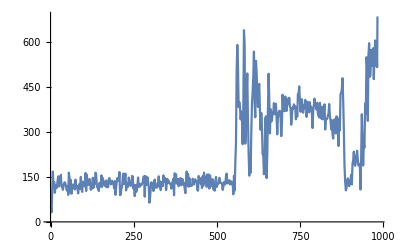

```mathematica
ListLinePlot[NIL1003Index3[[500]]]
```

```mathematica
Image[
normalizeAmplitudeOf2Darray[
NIL1003Index3
]
]
```

-Graphics-

#### saving *.xyz to disc

```mathematica
saveXYZforZygoProcessing[
(* xyz array *)imageDataToXYZ[
(* image array *)maskImageDataToPoints[
NIL1003Index3,
maskXstart,maskXend,
maskYstart,maskYend
]*1000(* nm to um *)
],
(* pixelSizeInNanometers *)31250,
(* fileNameAndPath *)ToString["E:\\ValsProjects\\SBIR_2022\\NASA_measurements\\ProcessignTests\\NIL1003.xyz"]
]
```

E:\ValsProjects\SBIR_2022\NASA_measurements\ProcessignTests\NIL1003.xyz

#### second dataset in the HDF5

```mathematica
NIL1003Index2=Import["E:\\ValsProjects\\SBIR_2022\\NASA_measurements\\NIL-Sample2-Concave-20221116-4.33X-Zoom\\NIL-Sample2-Concave-20221116-1003-4.33X-Zoom.h5",{"HDF5","Data",2(* third [second] dataset in the HDF5 file *)}];
```

```mathematica
dimensionsOfImageArrayData[NIL1003Index2]
```

{982,1003}

```mathematica
Image[
normalizeAmplitudeOf2Darray[
NIL1003Index2
]
]
```

-Graphics-

```mathematica
ListLinePlot[
NIL1003Index2[[500]]
]
```

-Graphics-

## NIL1005Index3

### NIL-Sample2-Concave-20221116-1005-4.33X-Zoom-Masked-5x5mm.h5

#### third dataset in the HDF5

```mathematica
NIL1005Index3=wavelengthCylindricalInterferometer*Import["E:\\ValsProjects\\SBIR_2022\\NASA_measurements\\NIL-Sample2-Concave-20221116-4.33X-Zoom\\NIL-Sample2-Concave-20221116-1005-4.33X-Zoom-Masked-5x5mm.h5",{"HDF5","Data",3(* third dataset in the HDF5 file *)}];
```

```mathematica
dimensionsOfImageArrayData[aFileMaybeIndex3]
```

{982,1003}

#### checking contents

```mathematica
Image[
normalizeAmplitudeOf2Darray[
aFileMaybeIndex3]
]
```

-Graphics-

#### saving *.xyz to disc

```mathematica
saveXYZforZygoProcessing[
(* xyz array *)imageDataToXYZ[
(* image array *)maskImageDataToPoints[
NIL1005Index3,
maskXstart,maskXend,
maskYstart,maskYend
]*1000(* nm to um *)
],
(* pixelSizeInNanometers *)31250,
(* fileNameAndPath *)ToString["E:\\ValsProjects\\SBIR_2022\\NASA_measurements\\ProcessignTests\\NIL1005.xyz"]
]
```

E:\ValsProjects\SBIR_2022\NASA_measurements\ProcessignTests\NIL1005.xyz

#### second dataset in the HDF5

```mathematica
aFileMaybeIndex2=Import["E:\\ValsProjects\\SBIR_2022\\NASA_measurements\\NIL-Sample2-Concave-20221116-4.33X-Zoom\\NIL-Sample2-Concave-20221116-1005-4.33X-Zoom-Masked-5x5mm.h5",{"HDF5","Data",2(* third [second] dataset in the HDF5 file *)}];
```

```mathematica
dimensionsOfImageArrayData[aFileMaybeIndex2]
```

{982,1003}

```mathematica
Image[normalizeAmplitudeOf2Darray[
aFileMaybeIndex2]
]
```

-Graphics-

## NIL1007Index3

### NIL-Sample2-Concave-20221116-1007-4.33X-Zoom-Unmasked.h5

#### third dataset in the HDF5

```mathematica
NIL1007Index3=wavelengthCylindricalInterferometer*Import["E:\\ValsProjects\\SBIR_2022\\NASA_measurements\\NIL-Sample2-Concave-20221116-4.33X-Zoom\\NIL-Sample2-Concave-20221116-1007-4.33X-Zoom-Unmasked.h5",{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}];
```

```mathematica
dimensionsOfImageArrayData[NIL1007Index3]
```

{982,1003}

#### checking contents

```mathematica
Image[
normalizeAmplitudeOf2Darray[
NIL1007Index3
]
]
```

-Graphics-

### Sub - area

#### portion of the full dataset

```mathematica
maskXstart=570;
maskXend=970;
maskYstart=435;
maskYend=635;
```

```mathematica
Image[
normalizeAmplitudeOf2Darray[
maskImageDataToPoints[
NIL1007Index3,
maskXstart,maskXend,
maskYstart,maskYend
]
]]
```

-Graphics-

```mathematica
imageDataToXYZ
```

```mathematica
maskImageDataToPoints[
NIL1007Index3,
maskXstart,maskXend,
maskYstart,maskYend
]
```

#### saving *.xyz to disc

```mathematica
saveXYZforZygoProcessing[
(* xyz array *)imageDataToXYZ[
(* image array *)maskImageDataToPoints[
NIL1007Index3,
maskXstart,maskXend,
maskYstart,maskYend
]*1000(* nm to um *)
],
(* pixelSizeInNanometers *)31250,
(* fileNameAndPath *)ToString["E:\\ValsProjects\\SBIR_2022\\NASA_measurements\\ProcessignTests\\NIL1007.xyz"]
]
```

E:\ValsProjects\SBIR_2022\NASA_measurements\ProcessignTests\NIL1007.xyz

#### slightly larger than patterned area

```mathematica
smallmaskXstart=110;
smallmaskXend=280;
smallmaskYstart=60;
smallmaskYend=150;

patternedRegionNIL107=maskImageDataToPoints[
maskImageDataToPoints[
NIL1007Index3,
maskXstart,maskXend,
maskYstart,maskYend
],
smallmaskXstart,smallmaskXend,
smallmaskYstart,smallmaskYend
]
```

```mathematica
dimensionsOfImageArrayData[
patternedRegionNIL107
]
```

{171,91}

```mathematica
Image[
normalizeAmplitudeOf2Darray[
patternedRegionNIL107]]
```

-Graphics-

#### patterned area

```mathematica
smallmaskXstart=115;
smallmaskXend=273;
smallmaskYstart=64;
smallmaskYend=145;

patternedRegionNIL107=maskImageDataToPoints[
maskImageDataToPoints[
NIL1007Index3,
maskXstart,maskXend,
maskYstart,maskYend
],
smallmaskXstart,smallmaskXend,
smallmaskYstart,smallmaskYend
];
```

```mathematica
dimensionsOfImageArrayData[
patternedRegionNIL107
]
```

{159,82}

```mathematica
Image[
normalizeAmplitudeOf2Darray[
patternedRegionNIL107
]]
```

-Graphics-

```mathematica
5/80//N
```

0.0625

```mathematica
5/160//N
```

0.03125

```mathematica
quickLookAtImageData[
patternedRegionNIL107
]
```

Fourier::fftl: Argument {0.0000648363+1.17354×10^-7 x+1/159 (-0.00839354-0.0000186593 x-0.000468032 y)+2.9436×10^-6 y,0.0000483863+1.17354×10^-7 x+1/159 (-0.00839354-0.0000186593 x-0.000468032 y)+2.9436×10^-6 y,«7»,8.24832×10^-6+1.17354×10^-7 x+1/159 (-0.00839354-0.0000186593 x-0.000468032 y)+2.9436×10^-6 y,«149»} is not a non-empty list or rectangular array of numeric quantities.

Drop::drop: Cannot drop positions -79 through -1 in Abs[Fourier[{0.0000648363+1.17354×10^-7 x+1/159 (-0.00839354-0.0000186593 x-0.000468032 y)+2.9436×10^-6 y,0.0000483863+1.17354×10^-7 x+1/159 (-0.00839354-0.0000186593 x-0.000468032 y)+2.9436×10^-6 y,«8»,«149»}]].

Fourier::fftl: Argument {0.0000385163+1.17354×10^-7 x+1/159 (-0.00931342-0.0000186593 x-0.000468032 y)+2.9436×10^-6 y,0.0000306203+1.17354×10^-7 x+1/159 (-0.00931342-0.0000186593 x-0.000468032 y)+2.9436×10^-6 y,«7»,0.0000141703+1.17354×10^-7 x+1/159 (-0.00931342-0.0000186593 x-0.000468032 y)+2.9436×10^-6 y,«149»} is not a non-empty list or rectangular array of numeric quantities.

Drop::drop: Cannot drop positions -79 through -1 in Abs[Fourier[{0.0000385163+1.17354×10^-7 x+1/159 (-0.00931342-0.0000186593 x-0.000468032 y)+2.9436×10^-6 y,0.0000306203+1.17354×10^-7 x+1/159 (-0.00931342-0.0000186593 x-0.000468032 y)+2.9436×10^-6 y,«8»,«149»}]].

Fourier::fftl: Argument {0.0000128543+1.17354×10^-7 x+1/159 (-0.0102761-0.0000186593 x-0.000468032 y)+2.9436×10^-6 y,0.0000135123+1.17354×10^-7 x+1/159 (-0.0102761-0.0000186593 x-0.000468032 y)+2.9436×10^-6 y,«7»,0.0000207503+1.17354×10^-7 x+1/159 (-0.0102761-0.0000186593 x-0.000468032 y)+2.9436×10^-6 y,«149»} is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

Drop::drop: Cannot drop positions -79 through -1 in Abs[Fourier[{0.0000128543+1.17354×10^-7 x+1/159 (-0.0102761-0.0000186593 x-0.000468032 y)+2.9436×10^-6 y,0.0000135123+1.17354×10^-7 x+1/159 (-0.0102761-0.0000186593 x-0.000468032 y)+2.9436×10^-6 y,«8»,«149»}]].

General::stop: Further output of Drop::drop will be suppressed during this calculation.

$Aborted

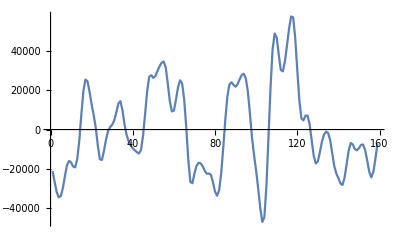

```mathematica
ListLinePlot[
detrendDatasetAndScale[
gaussianFilterDependentVectorOfTwoColumnDataset[
xTraceAtYpixelNumberFromImageFormattedData[
40,
patternedRegionNIL107
],
3],
1,10^9
]
]
```

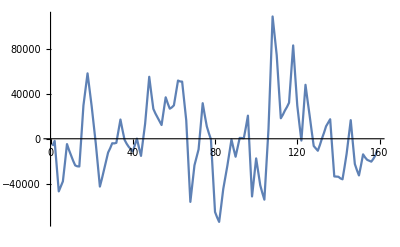

```mathematica
ListLinePlot[
detrendDatasetAndScale[
xTraceAtYpixelNumberFromImageFormattedData[
41,
patternedRegionNIL107
],
1,10^9
]
]
```

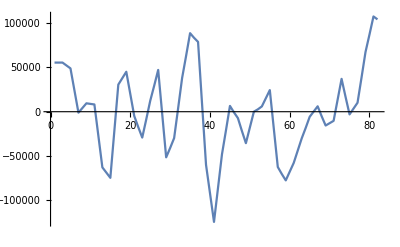

-Graphics-

```mathematica
ListLinePlot[
detrendDatasetAndScale[

yTraceAtXpixelNumberFromImageFormattedData[
80,
patternedRegionNIL107
],
1,10^9]
]
```

#### second dataset in the HDF5

```mathematica
unmasked4p33xIndex2=Import["E:\\ValsProjects\\SBIR_2022\\NASA_measurements\\NIL-Sample2-Concave-20221116-4.33X-Zoom\\NIL-Sample2-Concave-20221116-1007-4.33X-Zoom-Unmasked.h5",{"HDF5","Data",2(* third [second] dataset in the HDF5 file *)}];
```

```mathematica
Length[aFileMaybeIndex2]
```

1003

```mathematica
Length[aFileMaybeIndex2[[2]]]
```

982

```mathematica
Length[aFileMaybeIndex2[[3]]]
```

982

```mathematica
Length[aFileMaybeIndex2[[1]]]
```

982

```mathematica
Image[normalizeAmplitudeOf2Darray[
unmasked4p33xIndex3]
]
```

-Graphics-

## Scratchwork

```mathematica
1.4*10^-5/0.0457
```

0.000306346